Resources
https://mathematica.stackexchange.com/questions/268990/how-can-i-efficiently-calculate-exact-probability-distributions-for-dd-dice-lik

https://mathematica.stackexchange.com/questions/164151/combine-two-lists-with-all-possible-combinations

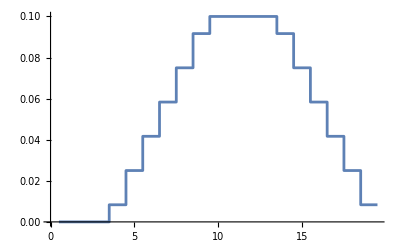

```mathematica
exactDice[sides_]:=∑_(n=1)^sides 1/sides x^(n)
diceList = {2,6, 10};
ndice=Length@diceList;
diceDistribution = Product[exactDice[d],{d, diceList}];
probs = CoefficientList[diceDistribution, x];
ListStepPlot[probs, Center]
```

A combination-based method. Create tuples to enumerate each possible roll. Sum. Count.

```mathematica
d6 = {1, 2, 3, 4, 5, 6};
d12 = {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12};
diceList = {d6, d6, -d6};
Times@@(Length/@diceList)
```

216

```mathematica
Length/@diceList
```

{6,6}

```mathematica
Total[Tuples[diceList],{2}]
```

{2,3,4,5,6,7,3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12}

This will count the number of occurrences.

```mathematica
Counts[Total[Tuples[diceList],{2}]]
```

<|1→21,0→15,-1→10,-2→6,-3→3,-4→1,2→25,3→27,4→27,5→25,6→21,7→15,8→10,9→6,10→3,11→1|>

```mathematica
Counts[Total[Tuples[diceList],{2}]]/(Times@@(Length/@diceList))
```

<|1→7/72,0→5/72,-1→5/108,-2→1/36,-3→1/72,-4→1/216,2→25/216,3→1/8,4→1/8,5→25/216,6→7/72,7→5/72,8→5/108,9→1/36,10→1/72,11→1/216|>

```mathematica
KeySort[%]
```

<|-4→1/216,-3→1/72,-2→1/36,-1→5/108,0→5/72,1→7/72,2→25/216,3→1/8,4→1/8,5→25/216,6→7/72,7→5/72,8→5/108,9→1/36,10→1/72,11→1/216|>

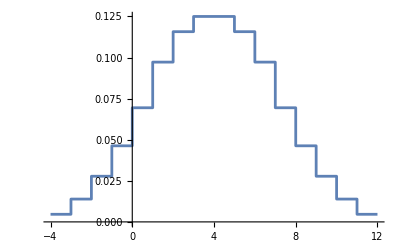

```mathematica
ListStepPlot[%]
```